```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

styles={Directive[RGBColor[0,0,0],AbsoluteThickness[3.5]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,1],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[2],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[2],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};

FrameTicksFontSize=16;
FrameFontSize=16;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->0.75,ImageSize->Medium,PlotStyle->styles,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];

Nf=3;
eg=16Pi^2/30;
eq=6*3*7Pi^2/120;  (*check these later*)
sFac = eg+eq ;

rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->1000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];
```

```mathematica
(*** e(T), P(T) lattice data ***)

eosDataRaw2=Import[wd<>"/best.dat"];
energy= eosDataRaw2[[1;;450,6]];
pressure=eosDataRaw2[[1;;450,3]];
entropy=eosDataRaw2[[1;;450,4]];
temp = 0.005067731*eosDataRaw2[[1;;450,2]]; (* convert units to fm^-1 *)

pressureTdata=Table[{temp[[i]],pressure[[i]]},{i,1,Length[pressure]}];
energyTdata=Table[{temp[[i]],energy[[i]]},{i,1,Length[energy]}];
entropyTdata=Table[{temp[[i]],entropy[[i]]},{i,1,Length[entropy]}];

edInt=Interpolation[energyTdata];
PInt=Interpolation[pressureTdata];
SInt=Interpolation[entropyTdata];

temp[[450]];
0.499*5.067731;
edInt[temp[[440]]]
PInt[temp[[440]]];
SInt[temp[[440]]]
(edInt[temp[[440]]]+PInt[temp[[440]]])/temp[[440]]
```

483.931

254.076

254.089

```mathematica
525.7510514039656
```

525.751

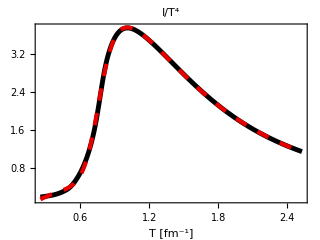

```mathematica
(*** Trace anomaly fit ***)

Inorm[T_]=(PInt'[T]/T^3-(4.0*PInt[T])/T^4);

Tmax =temp[[450]] ;
Tmin = temp[[1]];
dT = 0.01;
Tsteps = Floor[(Tmax-Tmin)/dT];
temp2=Table[Tmin+i*dT,{i,0,Tsteps}];

Inormdata=Table[{temp2[[i]],Inorm[temp2[[i]]]},{i,1,Length[temp2]}];

Clear[a0,h1,h2,h0,f0,f1,f2,g1,g2,Tc,T];

Tc=0.154*5.067731;
sol=FindFit[Inormdata,Exp[h1/(T/Tc)-h2/(T/Tc)^2]*(h0/(1.0+a0*(T/Tc)^2)+(f0*(Tanh[f1*(T/Tc)+f2]+1.0))/(1+g1*(T/Tc)+g2*(T/Tc)^2)),{h0,h1,h2,a0,f0,f1,f2,g1,g2},T,MaxIterations->20000];
h0=h0/.sol;
h1=h1/.sol;
h2=h2/.sol;
a0=a0/.sol;
f0=f0/.sol;
f1=f1/.sol;
f2=f2/.sol;
g1=g1/.sol;
g2=g2/.sol;
Inormfit[T_]=Exp[h1/(T/Tc)-h2/(T/Tc)^2]*(h0/(1.0+a0*(T/Tc)^2)+(f0*(Tanh[f1*(T/Tc)+f2]+1.0))/(1.0+g1*(T/Tc)+g2*(T/Tc)^2));

Plot[{Inorm[T],Inormfit[T]},{T,temp[[1]],temp[[450]]},PlotStyle->styles,PlotLabel->Style["I/T^4",FontSize->20],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]
```

4.89065×10^-8

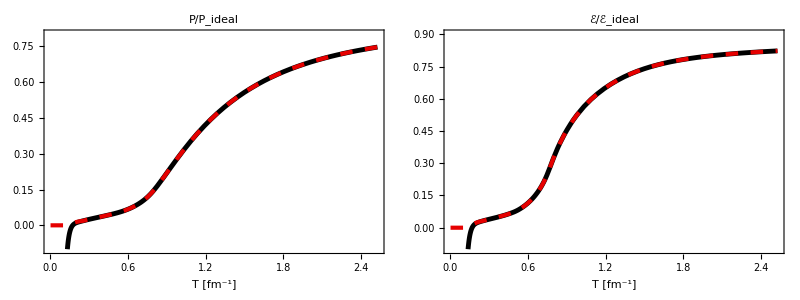

```mathematica
(* Fit e(T), P(T) to lower temperatures *)

(*Tmax=0.1;*)
Tmax=0.1;
Tmin = 0.001;
dT = 0.001;
Tsteps = Floor[(Tmax-Tmin)/dT];

temp2=Table[Tmin+i*dT,{i,0,Tsteps}];

Pfitdata=Table[{temp2[[i]],temp2[[i]]^4*(NIntegrate[Inormfit[Tp]/Tp,{Tp,0.0,temp2[[i]]}])},{i,1,Length[temp2]}];

efitdata=Table[{temp2[[i]],3.0*Pfitdata[[i,2]]+temp2[[i]]^4*Inormfit[temp2[[i]]]},{i,1,Length[temp2]}];

Ptotaldata=Join[Pfitdata,pressureTdata];
Pfit=Interpolation[Ptotaldata];

etotaldata=Join[efitdata,energyTdata];
efit=Interpolation[etotaldata];

(*Pfit=Interpolation[Pfitdata];
efit=Interpolation[efitdata];*)

efit[0.1]


Grid[{{Plot[{PInt[T]/(sFac T^4/3),Pfit[T]/(sFac T^4/3)},{T,0.001,temp[[450]]},PlotRange->{-0.1,0.8},PlotStyle->styles,PlotLabel->Style["P/P_ideal",FontSize->20],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{edInt[T]/(sFac T^4),efit[T]/(sFac T^4)},{T,0.001,temp[[450]]},PlotRange->{-0.1,0.9},PlotStyle->styles,PlotLabel->Style["ℰ/ℰ_ideal",FontSize->20],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

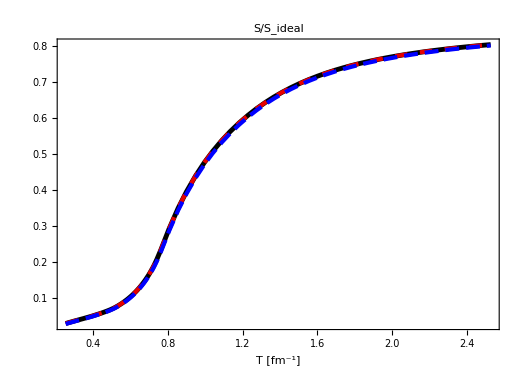

```mathematica
Sfit2[T_] = (efit[T]+Pfit[T])/T;

Sfit[T_]=Pfit'[T];



Plot[{SInt[T]/(4.0/3.0*sFac T^3),Sfit2[T]/(4.0/3.0*sFac T^3),PInt'[T]/(4.0/3.0*sFac T^3)},{T,temp[[1]],temp[[450]]},PlotRange->All,PlotStyle->styles,PlotLabel->Style["S/S_ideal",FontSize->20],ImageSize->520,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

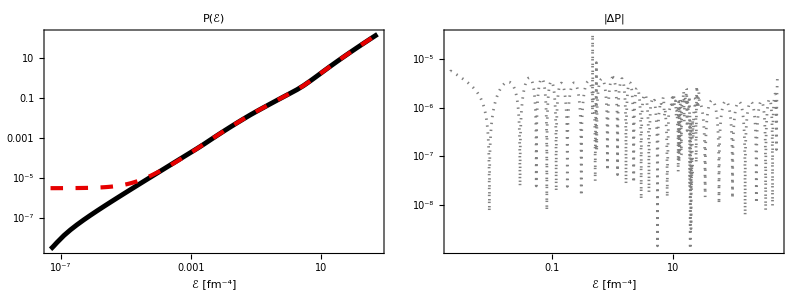

(-4.252354639211118e-8 - 0.0023401950204346624*e - 1.0202573531006838*Power(e,2) + 21.303008638448976*Power(e,3) - 179.02256153555777*Power(e,4) + 
     358.14756863054475*Power(e,5) + 347.2180474550277*Power(e,6) - 1439.7858205037123*Power(e,7) + 842.1715111012749*Power(e,8) + 164.54137445414798*Power(e,9) - 
     241.68615252464943*Power(e,10) + 147.98508035162953*Power(e,11) - 22.836140523100624*Power(e,12) + 10.400200205873778*Power(e,13) + 0.4564495736156534*Power(e,14) + 
     0.003915756908970399*Power(e,15) + 5.775328807317171e-6*Power(e,16))/
   (-0.013618039948887552 - 4.1884975304990695*e + 82.84864551906075*Power(e,2) - 614.6987351965184*Power(e,3) + 167.7178412315549*Power(e,4) + 6414.692315884927*Power(e,5) - 
     14283.472430729864*Power(e,6) + 10477.827407802211*Power(e,7) - 3335.755581712054*Power(e,8) + 939.1709961763124*Power(e,9) + 118.22913086465275*Power(e,10) + 
     31.820030616325298*Power(e,11) + 52.56369966539619*Power(e,12) + 1.7635640629427503*Power(e,13) + 0.013044952373045733*Power(e,14) + 0.00001789493029106512*Power(e,15) - 
     4.74803934553305e-11*Power(e,16))

```mathematica
(*** P(e) ***)

PdataED=Table[{efit[T],Pfit[T]},{T,0.1,temp[[450]],0.001}];
Pfunc=Interpolation[PdataED];

n =16;

PfitED[e_]=rationalPolyFit[PdataED,n,n]/.{x->e};

Grid[{{
LogLogPlot[{Pfunc[e],PfitED[e]},{e,efit[0.1],525.751},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["P(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLogPlot[{Abs[Pfunc[e]-PfitED[e]]},{e,efit[temp[[1]]],525.751},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|ΔP|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
CForm[PfitED[e]]
```

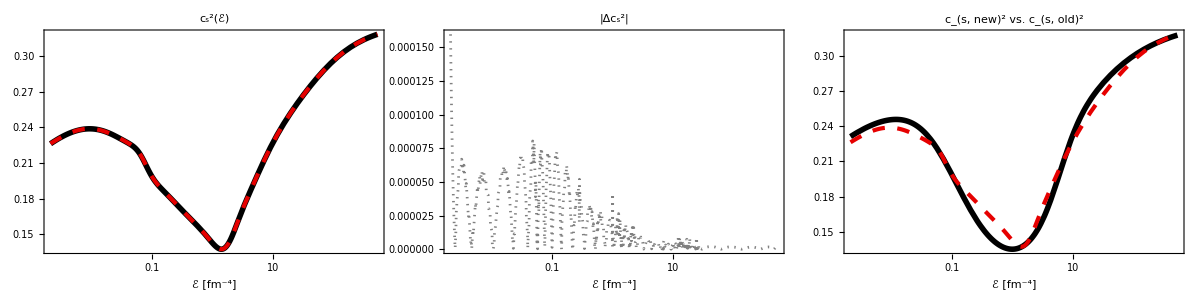

(0.000011268264457463064 + 0.006009019582224527*e - 0.07951153051224435*Power(e,2) - 1.1956738128979136*Power(e,3) + 33.482636499677014*Power(e,4) - 
     215.2517178513395*Power(e,5) + 672.184927569965*Power(e,6) - 1279.5359247672275*Power(e,7) + 1382.5611405253476*Power(e,8) - 854.2557836450292*Power(e,9) + 
     319.98761735384124*Power(e,10) - 65.52364329236023*Power(e,11) + 8.050166633698055*Power(e,12) + 0.36928084730512967*Power(e,13) + 0.0006888281760041592*Power(e,14))/
   (0.00005693142135846228 + 0.022695783077872397*e - 0.13832532095390018*Power(e,2) - 9.927341482212137*Power(e,3) + 195.26290985491676*Power(e,4) - 
     1144.7566052470877*Power(e,5) + 3342.9218324161106*Power(e,6) - 6029.402406921666*Power(e,7) + 5996.762044329188*Power(e,8) - 3350.406155930922*Power(e,9) + 
     1212.4830048383672*Power(e,10) - 245.66211313696488*Power(e,11) + 37.29731421204577*Power(e,12) + 1.1690939024156535*Power(e,13) + 0.0021047103832388513*Power(e,14))

```mathematica
(*** Subscript[c, s]^2(e) ***)

emin=0.0;
emax=efit[temp[[450]]];
(*
PdataED=Table[{efit[T],Pfit[T]},{T,0.008,temp[[400]],0.00001}];

Pfunc=Interpolation[PdataED];

Pfunc=Interpolation[PdataED];
*)

(*Subscript[c, s]^2 = dp/de = dp/dT dT/de = s dT/de= (e+p)/(T de/dT)*)
cs2temp[T_]=(efit[T]+Pfit[T])/(T*efit'[T]);

cs2original[T_]=(edInt[T]+PInt[T])/(T*edInt'[T]);

Plot[{cs2original[T],cs2temp[T]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["c_s^2(e)",FontSize->24],Axes->False,FrameLabel->{"e [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75];

cs2data=Table[{efit[T],cs2temp[T]},{T,1.001*temp[[1]],temp[[450]],0.0008}];

cs2=Interpolation[cs2data];

n =14;

cs2fit[e_]=rationalPolyFit[cs2data,n,n]/.{x->e};

cs2old[e_]=(5.191934309650155*10^-32+4.123605749683891*10^-23*e+3.1955868410879504*10^-16*e^2+1.4170364808063119*10^-10*e^3+6.087136671592452*10^-6*e^4+0.02969737949090831*e^5+15.382615282179595*e^6+460.6487249985994*e^7+1612.4245252438795*e^8+275.0492627924299*e^9+58.60283714484669*e^10+6.504847576502024*e^11+0.03009027913262399*e^12+8.189430244031285*10^-6*e^13)/(1.4637868900982493*10^-30+6.716598285341542*10^-22*e+3.5477700458515908*10^-15*e^2+1.1225580509306008*10^-9*e^3+0.00003551782901018317*e^4+0.13653226327408863*e^5+60.85769171450653*e^6+1800.5461219450308*e^7+15190.225535036281*e^8+590.2572000057821*e^9+293.99144775704605*e^10+21.461303090563028*e^11+0.09301685073435291*e^12+0.000024810902623582917*e^13);

Grid[{{
LogLinearPlot[{cs2[e],cs2fit[e]},{e,efit[temp[[1]]],emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_s^2(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLinearPlot[{Abs[cs2[e]-cs2fit[e]]},{e,efit[temp[[1]]],emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|Δc_s^2|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLinearPlot[{cs2old[e],cs2fit[e]},{e,efit[temp[[1]]],emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_(s, new)^2 vs. c_(s, old)^2",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

CForm[cs2fit[e]]
```

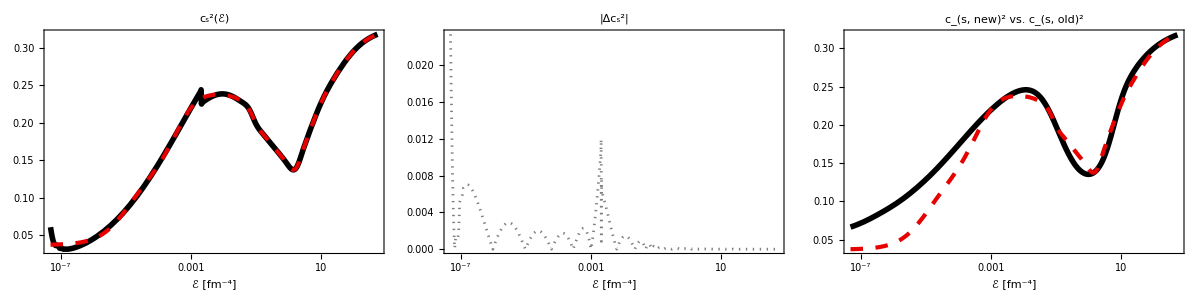

(1.8402520899108875e-11 + 6.236490812979835e-6*e + 0.030102633161530747*Power(e,2) + 31.28922210287743*Power(e,3) - 578.4206902547111*Power(e,4) + 
     4042.8118046589934*Power(e,5) - 3962.640748155799*Power(e,6) + 10446.164411025933*Power(e,7) - 7919.639983625435*Power(e,8) + 4148.342236482998*Power(e,9) - 
     197.63995666147952*Power(e,10) - 224.5031320579093*Power(e,11) + 105.82923062082472*Power(e,12) + 3.95243484853906*Power(e,13) + 0.0064980995386214055*Power(e,14))/
   (4.973236208999834e-10 + 0.00004875246783061799*e + 0.12819802371699762*Power(e,2) + 129.48439228429382*Power(e,3) - 2200.033654633667*Power(e,4) + 
     13154.226133440103*Power(e,5) + 13905.487800469253*Power(e,6) + 1328.3038118867867*Power(e,7) + 11691.365083487737*Power(e,8) + 2803.179071770458*Power(e,9) + 
     680.3049306463573*Power(e,10) - 499.4770623397496*Power(e,11) + 461.46954251159826*Power(e,12) + 12.474990300304118*Power(e,13) + 0.019844777924269252*Power(e,14))

```mathematica
emin=0.0;
emax=efit[temp[[450]]];

cs2temp[T_]=(efit[T]+Pfit[T])/(T*efit'[T]);


cs2data=Table[{efit[T],cs2temp[T]},{T,0.1,temp[[450]],0.0008}];

cs2=Interpolation[cs2data];

n =14;

cs2fit[e_]=rationalPolyFit[cs2data,n,n]/.{x->e};

cs2old[e_]=(5.191934309650155*10^-32+4.123605749683891*10^-23*e+3.1955868410879504*10^-16*e^2+1.4170364808063119*10^-10*e^3+6.087136671592452*10^-6*e^4+0.02969737949090831*e^5+15.382615282179595*e^6+460.6487249985994*e^7+1612.4245252438795*e^8+275.0492627924299*e^9+58.60283714484669*e^10+6.504847576502024*e^11+0.03009027913262399*e^12+8.189430244031285*10^-6*e^13)/(1.4637868900982493*10^-30+6.716598285341542*10^-22*e+3.5477700458515908*10^-15*e^2+1.1225580509306008*10^-9*e^3+0.00003551782901018317*e^4+0.13653226327408863*e^5+60.85769171450653*e^6+1800.5461219450308*e^7+15190.225535036281*e^8+590.2572000057821*e^9+293.99144775704605*e^10+21.461303090563028*e^11+0.09301685073435291*e^12+0.000024810902623582917*e^13);

Grid[{{
LogLinearPlot[{cs2[e],cs2fit[e]},{e,efit[0.1],emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_s^2(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLinearPlot[{Abs[cs2[e]-cs2fit[e]]},{e,efit[0.1],emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|Δc_s^2|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLinearPlot[{cs2old[e],cs2fit[e]},{e,efit[0.1],emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_(s, new)^2 vs. c_(s, old)^2",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

CForm[cs2fit[e]]
```

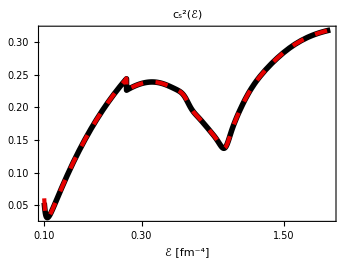

```mathematica
(** check chain rule in cs2 relations **)

LogLinearPlot[{cs2temp[T],cs2[efit[T]]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["c_s^2(ℰ)",FontSize->24],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

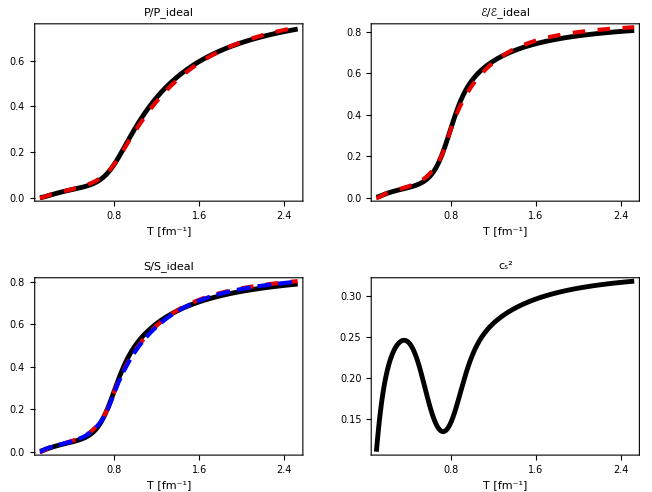

```mathematica
(*** Compare to old EOS data (black) ***)


eosDataRaw=Import[wd<>"/eos.dat"];
eosData= Take[eosDataRaw,{3,Length[eosDataRaw]}];
(* Subscript[ϵ, eq](T) *)
LogEDLogTInt = Interpolation[eosData[[All,{1,2}]]];
edIntold[T_] = 10^LogEDLogTInt[Log[10,T]];
(* Subscript[P, eq](T) *)
LogPLogTInt = Interpolation[eosData[[All,{1,4}]]];
PIntold[T_] = 10^LogPLogTInt[Log[10,T]];
(* Subscript[c, s]^2(T) *)
LogdPLogEdInt = Interpolation[eosData[[All,{2,5}]]];
dPIntE[e_]=10^LogdPLogEdInt[Log[10,e]];
LogdELogEdInt = Interpolation[eosData[[All,{2,3}]]];
dEIntE[e_]=10^LogdELogEdInt[Log[10,e]];
cs2Int[T_] = dPIntE[edIntold[T]]/dEIntE[edIntold[T]];

GraphicsGrid[{{Plot[{PIntold[T]/(sFac T^4/3),Pfit[T]/(sFac T^4/3)},{T,0.1,temp[[450]]},PlotStyle->styles,PlotLabel->Style["P/P_ideal",FontSize->24],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{edIntold[T]/(sFac T^4),efit[T]/(sFac T^4)},{T,0.1,temp[[450]]},PlotStyle->styles,PlotLabel->Style["ℰ/ℰ_ideal",FontSize->24],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]},
{Plot[{(edIntold[T]+PIntold[T])/(4.0/3.0*sFac T^4),(efit[T]+Pfit[T])/(4.0/3.0*sFac T^4),Pfit'[T]/(4.0/3.0*sFac T^3)},{T,0.1,temp[[450]]},PlotStyle->styles,PlotLabel->Style["S/S_ideal",FontSize->24],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{cs2Int[T],cs2temp[T]},{T,0.1,temp[[450]]},PlotStyle->styles,PlotLabel->Style["c_s^2",FontSize->24],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
```

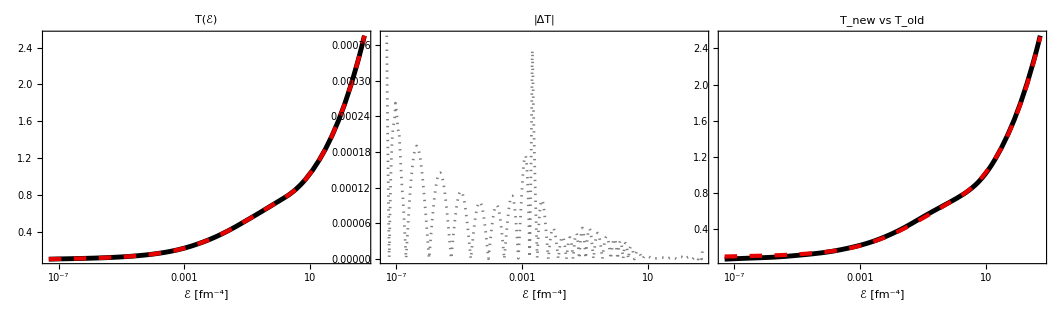

524.246

525.751

(1.5632496088409136e-21 + 1.3428093918763794e-14*e + 2.6698260471308687e-9*Power(e,2) + 0.00003397368068629029*Power(e,3) + 0.03344087886990132*Power(e,4) + 
     1.6621222298277474*Power(e,5) - 30.17007890494491*Power(e,6) + 1266.5888738256554*Power(e,7) + 5020.941469750197*Power(e,8) - 3594.180647667151*Power(e,9) + 
     1218.368476047873*Power(e,10) + 380.7181208450105*Power(e,11) + 11.483205968359934*Power(e,12) + 0.06238965622983938*Power(e,13) + 0.000045034652761739955*Power(e,14))/
   (1.6091573755001487e-20 + 1.2348780338596292e-13*e + 2.060058086975464e-8*Power(e,2) + 0.00019249168415972912*Power(e,3) + 0.11060137259953473*Power(e,4) + 
     2.1425360323788105*Power(e,5) - 33.920726078459296*Power(e,6) + 2574.2259352885526*Power(e,7) + 5876.618539369512*Power(e,8) - 4965.23518648975*Power(e,9) + 
     2046.626561462928*Power(e,10) + 341.7718938542966*Power(e,11) + 6.899257418668784*Power(e,12) + 0.02413844333527999*Power(e,13) + 8.955458570934743e-6*Power(e,14))

```mathematica
(*** T(e) ***)
emin=efit[0.1];
emax=efit[temp[[450]]];

efit[0.155*5.067731];

TdataED=Table[{efit[T],T},{T,0.1,temp[[450]],0.0008}];

Tfunc=Interpolation[TdataED];

n =14;

Tfit[e_]=rationalPolyFit[TdataED,n,n]/.{x->e};

Told[e_]=(2.059151308901543*10^-66+1.2883117551723254*10^-37*e+9.653685304732326*10^-18*e^2+0.0021387548523685764*e^3+3.152348276671561*10^7*e^4+6.128861811040275*10^14*e^5+1.2611913502159628*10^20*e^6+8.510311640702168*10^23*e^7+3.3406440917885196*10^26*e^8+9.526824863039937*10^27*e^9-5.540454604707275*10^27*e^10-3.834326779020863*10^28*e^11+2.732286036998176*10^28*e^12+3.389763887380034*10^27*e^13+3.271304177799644*10^25*e^14+3.5796316255209677*10^22*e^15+3.647754101481452*10^18*e^16)/(3.465150960288193*10^-64+7.292333136125966*10^-36*e+3.167120708990754*10^-16*e^2+0.047875501682141906*e^3+5.1924910033740276*10^8*e^4+7.186120863411006*10^15*e^5+9.741960860767537*10^20*e^6+3.9749426686364564*10^24*e^7+9.163047659503782*10^26*e^8+1.4902973847933083*10^28*e^9-1.710867316101183*10^28*e^10-4.366544624555957*10^28*e^11+3.801696016710178*10^28*e^12+2.43514662137169*10^27*e^13+1.376570820431094*10^25*e^14+8.761759990161081*10^21*e^15+4.265493796252328*10^17*e^16);

GraphicsGrid[{{
LogLinearPlot[{Tfunc[e],Tfit[e]},{e,efit[0.1],emax},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["T(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],

LogLinearPlot[{Abs[Tfunc[e]-Tfit[e]]},{e,efit[0.1],emax},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["|ΔT|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],

LogLinearPlot[{Told[e],Tfit[e]},{e,efit[0.1],emax},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["T_new vs T_old",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}},Spacings->{-50,0}]

edIntold[temp[[450]]+0.01]
efit[temp[[450]]]

CForm[Tfit[e]]
```

1.37653

1.37651

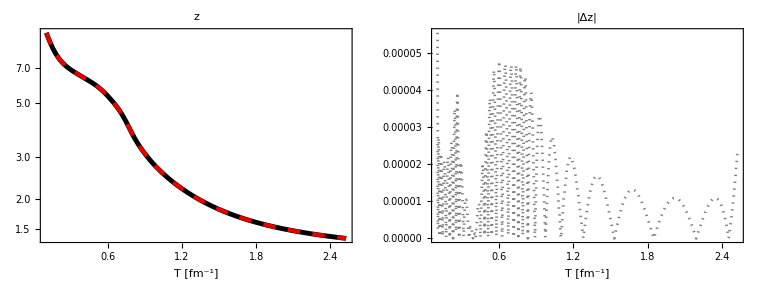

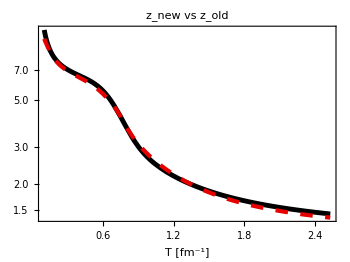

(0.0063989279669022965 - 0.129859006172768*T + 1.2375987648563989*Power(T,2) - 7.08677160437318*Power(T,3) + 25.522163486069513*Power(T,4) - 53.39704817423931*Power(T,5) + 
     35.56732439432871*Power(T,6) + 131.4191112968644*Power(T,7) - 456.33165080964596*Power(T,8) + 732.731408345977*Power(T,9) - 725.7680196237106*Power(T,10) + 
     463.5112126421111*Power(T,11) - 181.3140578574719*Power(T,12) + 34.70969629960206*Power(T,13) - 0.6279692610417852*Power(T,14))/
   (0.00042645826163359993 - 0.006176099195204174*T + 0.028274661507864094*Power(T,2) + 0.11033348820378089*Power(T,3) - 2.3302954492676218*Power(T,4) + 
     15.979722761706626*Power(T,5) - 65.81729691435565*Power(T,6) + 181.9339778552323*Power(T,7) - 351.62220585222946*Power(T,8) + 481.50598583127504*Power(T,9) - 
     462.3808537498894*Power(T,10) + 298.15143462767634*Power(T,11) - 115.90199093573125*Power(T,12) + 19.923926121264586*Power(T,13) + 0.4431361984724655*Power(T,14))

```mathematica
(*** z(T) ***)

Sfit[T_] = (efit[T]+Pfit[T])/T;

(*Sfit[T_]=Pfit'[T];*)

nc = 3.0;
nf = 3.0;
g =Pi^4/180.0*(4.0*(nc^2-1.0)+7.0*nc*nf);
F[T_]=(2.0*Pi^2)/g*Sfit[T]/T^3;


Tmax =temp[[450]] ;
Tmin =temp[[1]];
dT = 0.001;
Tsteps = Floor[(Tmax-Tmin)/dT];
temp2=Table[Tmin+i*dT,{i,0,Tsteps}];


zQuasi=Table[{temp2[[i]],""},{i,1,Length[temp2]}];

zQuasi[[Length[zQuasi],2]]=x/.FindRoot[x^3*BesselK[3,x]==F[temp[[450]]],{x,1.0},MaxIterations->5000]

For[i = Length[zQuasi]-1, i >0,i--,
zQuasi[[i,2]]=x/.FindRoot[x^3*BesselK[3,x]==F[zQuasi[[i,1]]],{x,zQuasi[[i+1,2]]},MaxIterations->5000];
]

zQuasifunc=Interpolation[zQuasi];


zQuasidata=Table[{T,zQuasifunc[T]},{T,0.1,temp[[450]],0.0008}];

n = 14;

zQuasifit[T_]=rationalPolyFit[zQuasidata,n,n]/.{x->T};

zQuasifit[temp[[450]]]


zold[T_]=(2.195527549421445*10^-14+5.014273212142939*10^-11*T+6.8769768080936324*10^-9*T^2-1.3090323372462384*10^-6*T^3+0.00007503723419734601*T^4-0.0019335423100477788*T^5+0.0077581370622797526*T^6+1.0840238709953247*T^7-40.41237726417249*T^8+815.5709414412947*T^9-11117.3113417968*T^10+107720.35990943392*T^11-727161.0603316505*T^12+3.12288627176472*10^6*T^13-7.240727201149486*10^6*T^14+8.813651470346985*10^6*T^15-3.535759885234317*10^6*T^16-5.454281769326236*10^6*T^17+1.0415987187648855*10^7*T^18-8.0189396235499745*10^6*T^19+2.6430627991581215*10^6*T^20)/(1.1541703277540495*10^-16+4.122377967105372*10^-13*T+1.2528690762234088*10^-10*T^2-1.1203883703791743*10^-8*T^3-3.65428489042621*10^-8*T^4+0.00004068369176438496*T^5-0.0024580222716044254*T^6+0.08433957015198745*T^7-2.0279246693088906*T^8+36.56366190486074*T^9-490.05025567116945*T^10+4477.3308927313055*T^11-21467.525530376926*T^12-23929.310531648207*T^13+889228.088912891*T^14-4.262596231414713*10^6*T^15+1.0642287968093066*10^7*T^16-1.643826578603126*10^7*T^17+1.6160269998993594*10^7*T^18-9.40765741315934*10^6*T^19+2.502796051035953*10^6*T^20);

GraphicsGrid[{{
LogPlot[{zQuasifunc[T],zQuasifit[T]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["z",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{Abs[zQuasifunc[T]-zQuasifit[T]]},{T,0.1,0.999temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δz|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

LogPlot[{zold[T],zQuasifit[T]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["z_new vs z_old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]

zQuasifit[T]//CForm
```

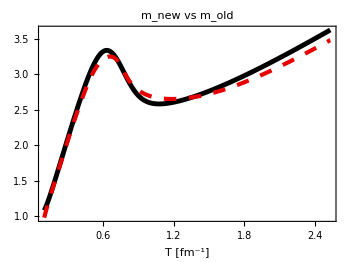

```mathematica
mQuasifunc[T_] =T*zQuasifunc[T]; 

Plot[{T*zold[T],mQuasifunc[T]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["m_new vs m_old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

```mathematica
(*** m(e) and dm/de ***) 

mdataED=Table[{efit[T],T*zQuasifunc[T]},{T,temp[[1]],temp[[450]],0.0006}];

mfunc=Interpolation[mdataED];

mdmde[e_]=mfunc[e]*mfunc'[e];

mdmdedata=Table[{efit[T],mdmde[efit[T]]},{T,temp[[1]],temp[[450]],0.0006}];

n =18;

mdmdefit[e_]=rationalPolyFit[mdmdedata,n,n]/.{x->e};

mdmdeold[e_]=(1.0932938963420931*10^-38-1.007252920091783*10^-31*e+1.258073500377669*10^-25*e^2+3.7902939287037426*10^-19*e^3+9.982754875153906*10^-14*e^4+5.356830067926448*10^-9*e^5+0.00006631556444292836*e^6+0.19429591145238154*e^7+133.14135704995198*e^8+19906.496386848434*e^9+468502.08289765124*e^10-2.1057407552865325*10^6*e^11-3.1682608543291925*10^6*e^12+1.7046132756833293*10^7*e^13-1.3636657914477058*10^7*e^14+2.0863251242849804*10^7*e^15-2.0496583087455064*10^7*e^16-4.069098068002096*10^7*e^17+3.445677209399048*10^7*e^18-3.7295352481362685*10^6*e^19+212848.6045508894*e^20-15965.651067054185*e^21+532.5403558600549*e^22+2.411729540242231*e^23+0.00027216645617684197*e^24)/(1.8097473184974786*10^-43-1.1919700038034044*10^-36*e-2.880545193459095*10^-30*e^2+1.5774335161251585*10^-23*e^3+1.2056411612584795*10^-17*e^4+1.5859303052883873*10^-12*e^5+4.642427449619644*10^-8*e^6+0.0003211322658208788*e^7+0.5307842016671973*e^8+205.22641687449376*e^9+17197.020001063076*e^10+262076.7134892617*e^11+1.517168279215402*10^6*e^12-4.41387607180566*10^6*e^13-4.689689648983293*10^6*e^14-1.1727564734279385*10^6*e^15+4.517859607565268*10^6*e^16+1.8472203478591543*10^7*e^17+1.8233835956962608*10^7*e^18-2.052678068458237*10^7*e^19+1.7590273805695719*10^6*e^20-448178.89154244727*e^21+13727.684912668212*e^22+572.3076682226775*e^23+0.5135708549693685*e^24);


Grid[{{LogLogPlot[{Abs[mdmde[e]],Abs[mdmdefit[e]]},{e,0.01,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLinearPlot[{Abs[mdmde[e]-mdmdefit[e]]},{e,0.01,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δmdm/dℰ|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

LogLogPlot[{Abs[mdmdeold[e]],Abs[mdmdefit[e]]},{e,0.01,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]

mdmdefit[e]//CForm
```

LogLogPlot[{Abs[mdmde[e]],Abs[mdmdefit[e]]},{e,0.01,emax},PlotStyle→styles,ImageSize→350,Frame→True,PlotLabel→mdm/dℰ,Axes→False,FrameLabel→{ℰ [fm^-4],},BaseStyle→{FontSize→16},AspectRatio→0.75] | LogLinearPlot[{Abs[mdmde[e]-mdmdefit[e]]},{e,0.01,emax},PlotStyle→styles,ImageSize→350,Frame→True,PlotLabel→|Δmdm/dℰ|,Axes→False,FrameLabel→{ℰ [fm^-1],},BaseStyle→{FontSize→16},AspectRatio→0.75]

LogLogPlot[{Abs[mdmdeold[e]],Abs[mdmdefit[e]]},{e,0.01,emax},PlotStyle→styles,ImageSize→350,Frame→True,PlotLabel→mdm/dℰ,Axes→False,FrameLabel→{ℰ [fm^-4],},BaseStyle→{FontSize→16},AspectRatio→0.75]

(3.733848972964999e-6 + 0.0022950340541103135*e + 0.05743710045877557*Power(e,2) - 4.432216849429155*Power(e,3) + 112.95167057993312*Power(e,4) - 
     1383.3168816540474*Power(e,5) + 9284.882181955134*Power(e,6) - 25365.229151656436*Power(e,7) + 18466.33819530928*Power(e,8) + 27136.016411750814*Power(e,9) - 
     56694.51741674112*Power(e,10) + 64282.80926298541*Power(e,11) - 54824.40417491978*Power(e,12) + 21562.414457373157*Power(e,13) - 3842.736715678516*Power(e,14) + 
     90.69178470319886*Power(e,15) + 31.540258522154648*Power(e,16) - 1.453458033179016*Power(e,17) - 0.0003263733495691238*Power(e,18))/
   (2.898602159235197e-9 + 0.000012089590286866211*e + 0.0026128449834450485*Power(e,2) + 0.0041016266976823795*Power(e,3) - 1.795429819022389*Power(e,4) + 
     43.82036964755872*Power(e,5) - 369.0689163344265*Power(e,6) + 1026.4794248711985*Power(e,7) + 12209.809748514597*Power(e,8) - 40403.09976104377*Power(e,9) + 
     20040.042629125142*Power(e,10) + 13263.21475259067*Power(e,11) + 6064.663930653264*Power(e,12) - 29393.37310427225*Power(e,13) + 28388.35166449818*Power(e,14) - 
     11089.861826510401*Power(e,15) + 2126.7170218137003*Power(e,16) - 142.54648405126042*Power(e,17) - 0.550065107893334*Power(e,18))

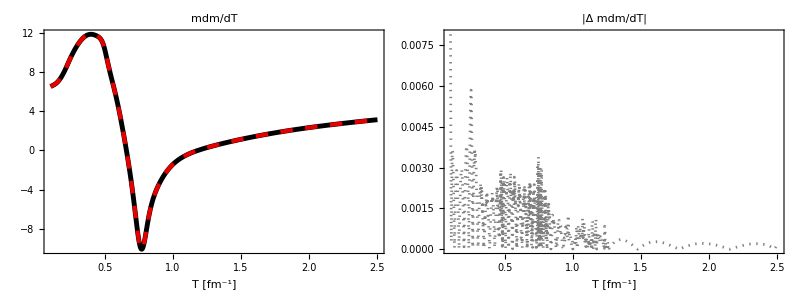

(0.005688116310212375 - 0.14611868522620855*T + 1.7418346790224628*Power(T,2) - 12.683060402707596*Power(T,3) + 62.827750357415525*Power(T,4) - 
     223.80105581429635*Power(T,5) + 591.540829696673*Power(T,6) - 1180.5722821169313*Power(T,7) + 1792.691727086785*Power(T,8) - 2069.8063224024963*Power(T,9) + 
     1800.2457307093605*Power(T,10) - 1156.0713870248137*Power(T,11) + 528.5337493913634*Power(T,12) - 160.98572138557043*Power(T,13) + 28.47019067060711*Power(T,14) - 
     1.9094581133029351*Power(T,15) - 0.0821052871841987*Power(T,16))/
   (0.0009134592615761402 - 0.023808961385213857*T + 0.2886290320476505*Power(T,2) - 2.1465858065914083*Power(T,3) + 10.918274379649286*Power(T,4) - 
     40.16300797581483*Power(T,5) + 110.29595577377587*Power(T,6) - 230.22782075546658*Power(T,7) + 368.3930002156695*Power(T,8) - 452.20545313176035*Power(T,9) + 
     422.8875894543935*Power(T,10) - 296.5348750714594*Power(T,11) + 151.575010750917*Power(T,12) - 53.83998777771685*Power(T,13) + 12.217572405731278*Power(T,14) - 
     1.5003634520298057*Power(T,15) + 0.0649648846785066*Power(T,16))

```mathematica
(*** m dm/dT ***) 

mQuasifunc[T_] =T*zQuasifunc[T]; 

mdmdTQuasi[T_] = mQuasifunc[T] *D[ mQuasifunc[T],T];

(*mdmdTQuasi[T_] = mQuasifunc[T]*(zQuasifunc[T]+T*zQuasifunc'[T]);*)

mdmdTQuasidata=Table[{T,mdmdTQuasi[T]},{T,0.1,temp[[450]],0.001}];

n = 16;

mdmdTQuasifit[T_]=rationalPolyFit[mdmdTQuasidata,n,n]/.{x->T};
Grid[{{
Plot[{mdmdTQuasi[T],mdmdTQuasifit[T]},{T,0.1,0.99temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dT",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[mdmdTQuasi[T]-mdmdTQuasifit[T]]},{T,0.1,0.99temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δ mdm/dT|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

mdmdTQuasifit[T]//CForm
```

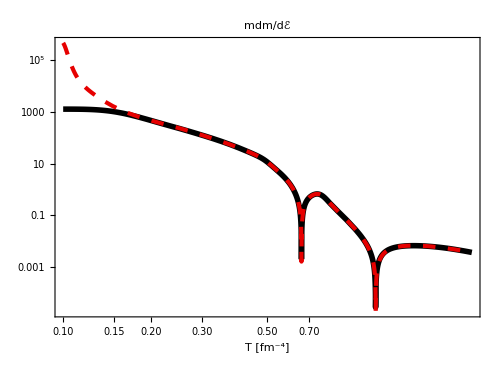

```mathematica
(*** check chain rule in relation: dm/de = cs2/s dm/dT ***)

LogLogPlot[{Abs[mdmdefit[efit[T]]],Abs[cs2fit[efit[T]]/Sfit[T]*mdmdTQuasifit[T]]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->500,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->24],Axes->False,FrameLabel->{"T [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

-10.871

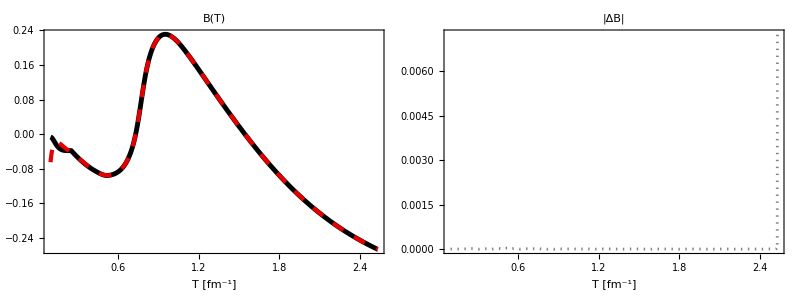

(0.001807173915691185 - 0.09859621834410072*T + 1.8376016181422836*Power(T,2) - 17.396228032936282*Power(T,3) + 97.24189906164712*Power(T,4) - 351.2275946061169*Power(T,5) + 
     858.5738316427057*Power(T,6) - 1451.1443152779416*Power(T,7) + 1697.5385173030693*Power(T,8) - 1343.2823713233752*Power(T,9) + 679.147270073541*Power(T,10) - 
     194.69714953534807*Power(T,11) + 23.571465826229385*Power(T,12))/
   (62.29289023037758 - 662.8507951050497*T + 3193.609224827773*Power(T,2) - 9062.910870152964*Power(T,3) + 16719.65665025377*Power(T,4) - 21040.559913433863*Power(T,5) + 
     18512.404218345502*Power(T,6) - 11495.040995425552*Power(T,7) + 5009.989934313891*Power(T,8) - 1496.8162171829113*Power(T,9) + 292.7822917889345*Power(T,10) - 
     34.043147290221185*Power(T,11) + 1.779696901838548*Power(T,12))

```mathematica
(*** Subscript[B, eq](T) ***)

dmdTQuasi[T_]=mQuasifunc'[T];


(*H[T_] := -(g*T^3*zQuasifunc[T]^2*BesselK[1,zQuasifunc[T]]*dmdTQuasi[T])/(2.0*Pi^2);*)

(*H[T_] := -(g*T^3*mQuasifunc[T]*BesselK[1,zQuasifunc[T]]*mdmdTQuasifit[T])/(2.0*T^2*Pi^2);*)


H[T_] = Sfit[T]-Pfit'[T]-(g*T^3*zQuasifunc[T]^2*BesselK[1,zQuasifunc[T]]*dmdTQuasi[T])/(2.0*Pi^2);

HQuasi=Table[{T,""},{T,0.001,temp[[450]],0.001}];
B0Quasi=Table[{T,""},{T,0.001,temp[[450]],0.001}];

For[i = 1, i ≤Length[HQuasi],i++,

Tprime = HQuasi[[i,1]];
HQuasi[[i,2]]= H[Tprime];
]

Hfunc=Interpolation[HQuasi];

B0Quasi[[1,2]] = 0.0;

For[i = 2, i ≤Length[B0Quasi],i++,
B0Quasi[[i,2]]= B0Quasi[[i-1,2]] + NIntegrate[Hfunc[Tprime],{Tprime,B0Quasi[[i-1,1]],B0Quasi[[i,1]]},AccuracyGoal->8];
]

B0Quasifunc=Interpolation[B0Quasi];

n = 12;

B0Quasi=Table[{T,B0Quasifunc[T]},{T,0.01,temp[[450]],0.001}];

B0Quasifunc=Interpolation[B0Quasi];

B0Quasifit[T_]=rationalPolyFit[B0Quasi,n,n]/.{x->T};

B0Quasifit[temp[[450]]]

Grid[{{
Plot[{B0Quasifunc[T]/T^4,B0Quasifit[T]/T^4},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[B0Quasifunc[T]-B0Quasifit[T]]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔB|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

B0Quasifit[T]//CForm
```

-10.871

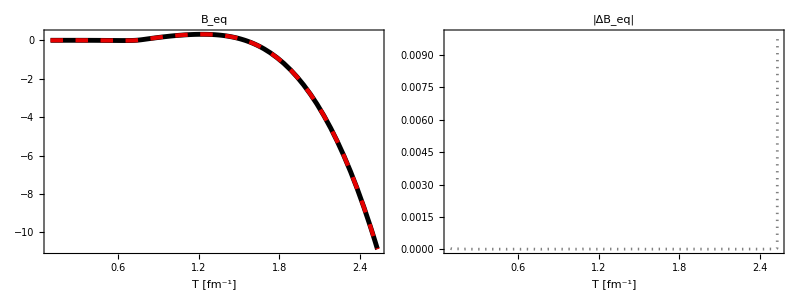

(0.049876854101214486 - 1.409808453961452*T + 16.939176071815616*Power(T,2) - 114.93699202937512*Power(T,3) + 492.1260376379328*Power(T,4) - 1412.0939018697075*Power(T,5) + 
     2811.730953466034*Power(T,6) - 3950.3001690995143*Power(T,7) + 3911.470068101795*Power(T,8) - 2667.688524007832*Power(T,9) + 1185.5194934056626*Power(T,10) - 
     305.36281110670285*Power(T,11) + 33.99720218416452*Power(T,12))/
   (83.15180291058289 - 887.5735618806963*T + 4176.224219061143*Power(T,2) - 11440.707121184269*Power(T,3) + 20314.664132634087*Power(T,4) - 24640.762855795965*Power(T,5) + 
     20962.823105356358*Power(T,6) - 12626.993051529775*Power(T,7) + 5352.796848516807*Power(T,8) - 1559.727198028125*Power(T,9) + 298.6994198022604*Power(T,10) - 
     34.18050916462276*Power(T,11) + 1.7646242258906506*Power(T,12))

```mathematica
(*** Subscript[B, eq](T) alternative ***)

n = 12;

Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];

B0Quasi2=Table[{T,Pquasi[T]-Pfit[T]},{T,0.1,temp[[450]],0.0008}];

B0Quasifunc2=Interpolation[B0Quasi2];

B0Quasifit2[T_]=rationalPolyFit[B0Quasi2,n,n]/.{x->T};

B0Quasifit2[temp[[450]]]

Grid[{{
Plot[{B0Quasifunc2[T],B0Quasifit2[T]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[B0Quasifunc2[T]-B0Quasifit2[T]]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔB_eq|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

B0Quasifit2[T]//CForm

(* It's probably more accurate to calculate B this way *)
```

-InterpolatingFunction[{{0.001,2.5288}},<>][T]-InterpolatingFunction[{{0.01,2.528}},<>][T]+10.4179 T^3 BesselK[2,InterpolatingFunction[{{0.253387,2.52839}},<>][T]] (InterpolatingFunction[{{0.253387,2.52839}},<>][T])^2+5.20896 T^4 BesselK[2,InterpolatingFunction[{{0.253387,2.52839}},<>][T]] InterpolatingFunction[{{0.253387,2.52839}},<>][T] InterpolatingFunction[{{0.253387,2.52839}},<>][T]+1.30224 T^4 (-BesselK[1,InterpolatingFunction[{{0.253387,2.52839}},<>][T]]-BesselK[3,InterpolatingFunction[{{0.253387,2.52839}},<>][T]]) (InterpolatingFunction[{{0.253387,2.52839}},<>][T])^2 InterpolatingFunction[{{0.253387,2.52839}},<>][T]

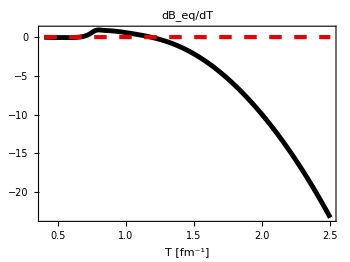

```mathematica
dmdTQuasi[T_]=mQuasifunc'[T];

mold[T_]=T*zold[T];

dmdTold[T_]=mold'[T];

(*H[T_] = -(g*T^3*zQuasifunc[T]^2*BesselK[1,zQuasifunc[T]]*dmdTQuasi[T])/(2.0*Pi^2);*)
(*H[T_] = -(g*T^3*zQuasifit[T]^2*BesselK[1,zQuasifit[T]]*dmdTQuasi[T])/(2.0*Pi^2);*)

H[T_] = -(g*T*mQuasifunc[T]*BesselK[1,zQuasifit[T]]*mdmdTQuasi[T])/(2.0*Pi^2);


H2[T_]=D[Pquasi[T]-Pfit[T],T]

Hfuncold[T_]=-(g*T^3*zold[T]^2*BesselK[1,zold[T]]*dmdTold[T])/(2.0*Pi^2);

Plot[{H[T],H2[T]},{T,.4,0.99temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["dB_eq/dT",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

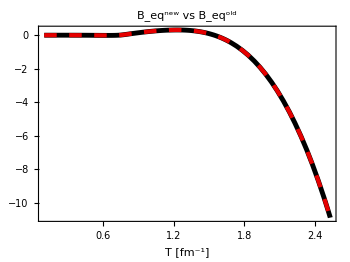

```mathematica
Beqold[T_]=(-0.003259287424704517+0.4709321130178677*T-18.471027719937705*T^2+334.0690722721871*T^3-3454.385244668648*T^4+22960.15979638924*T^5-105315.46668675772*T^6+346561.90522823617*T^7-836638.407629094*T^8+1.501743414016609*10^6*T^9-2.020237220416*10^6*T^10+2.0480693209160143*10^6*T^11-1.5779382837830463*10^6*T^12+943559.9448756306*T^13-456516.3985230772*T^14+185756.11302939596*T^15-61106.69072505601*T^16+13705.921942194844*T^17-1465.8180676090112*T^18)/(294.675932969415-1745.8088045773043*T+3997.025794070807*T^2-3586.7652790072334*T^3-1117.8588245192668*T^4+3765.9359654630407*T^5+841.4750390325167*T^6-4142.400568278239*T^7-1464.515167915579*T^8+4738.833500521431*T^9+2188.180519746309*T^10-6031.500378704362*T^11-203.76274436224986*T^12+5225.119313817963*T^13-3608.5761295285674*T^14+927.278254033823*T^15-80.77885500958108*T^16+4.197658993150538*T^17-0.10024694968615945*T^18);

Plot[{B0Quasifit[T],B0Quasifit2[T]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq^new vs B_eq^old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

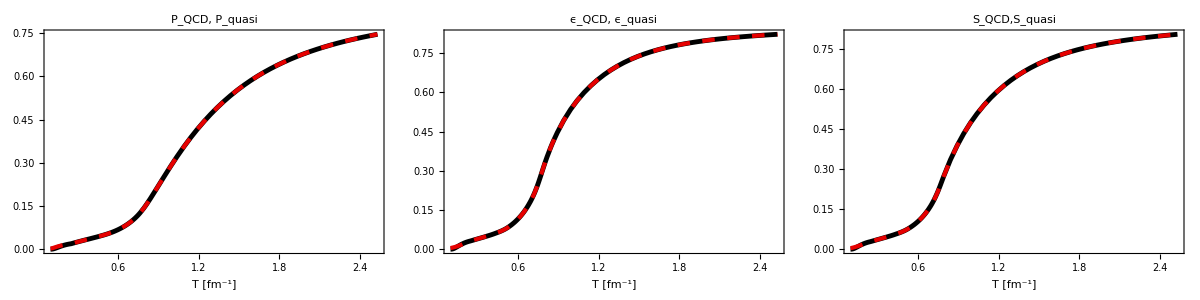

```mathematica
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]] -B0Quasifunc[T];
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]])+B0Quasifunc[T];

SQuasi[T_]=(Pquasi[T]+Equasi[T])/T;

Grid[{{Plot[{Pfit[T]/(sFac T^4/3),Pquasi[T]/(sFac T^4/3)},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD, P_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{efit[T]/(sFac T^4),Equasi[T]/(sFac T^4)},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD, ϵ_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Sfit[T]/(4*sFac*T^3/3),SQuasi[T]/(4*sFac*T^3/3)},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"S_QCD,S_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

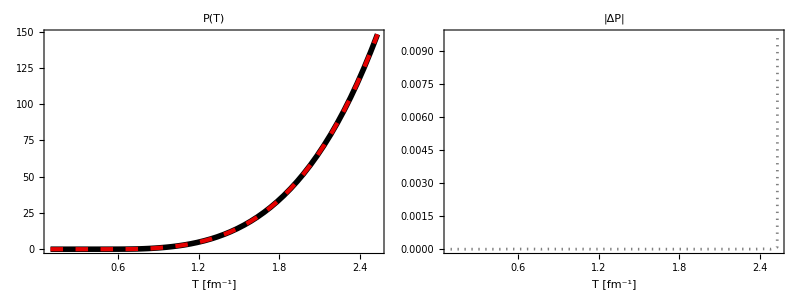

(0.0010834032370871081 - 0.04449924423833296*T + 0.7987239281723152*Power(T,2) - 8.293457396041585*Power(T,3) + 55.47747592468854*Power(T,4) - 251.8008027434223*Power(T,5) + 
     798.0276315065619*Power(T,6) - 1789.2254315087637*Power(T,7) + 2831.7359134139706*Power(T,8) - 3099.056559587395*Power(T,9) + 2234.118419109557*Power(T,10) - 
     955.3439881435701*Power(T,11) + 183.71527114069616*Power(T,12))/
   (2.567852274145253 - 24.358796265668467*T + 95.98202953147899*Power(T,2) - 196.7644974572158*Power(T,3) + 195.87797432398887*Power(T,4) + 9.617396045246277*Power(T,5) - 
     291.0495948650803*Power(T,6) + 401.52660407475486*Power(T,7) - 288.43502272805006*Power(T,8) + 118.94382423576974*Power(T,9) - 27.262122984949393*Power(T,10) + 
     3.6311987418815317*Power(T,11) - 0.21431158618845222*Power(T,12))

```mathematica
(* Fitting the quasiparticle kinetic pressure (B = 0) *)
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];  (*kinetic only; no bag term*)
Pquasidata=Table[{T,Pquasi[T]},{T,0.1,temp[[450]],0.0008}];
n = 12;
Pquasifit[T_]=rationalPolyFit[Pquasidata,n,n]/.{x->T};

Grid[{{
Plot[{Pquasi[T],Pquasifit[T]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["P(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Pquasi[T]-Pquasifit[T]]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔP|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
Pquasifit[T]//CForm
```

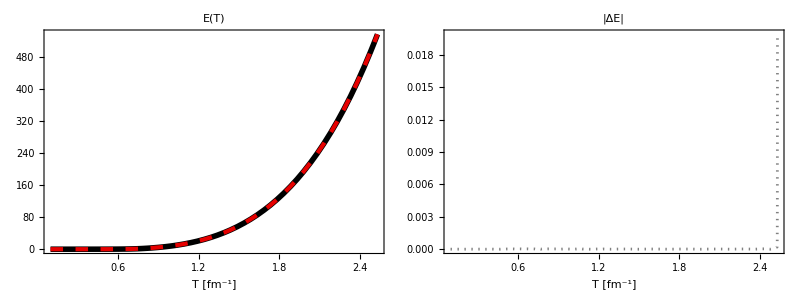

(0.0011430080199263993 - 0.05419274289028525*T + 1.104342959745772*Power(T,2) - 12.806832972574947*Power(T,3) + 93.88313006441084*Power(T,4) - 456.58669091770423*Power(T,5) + 
     1521.327077570759*Power(T,6) - 3537.8448624955636*Power(T,7) + 5756.389224516078*Power(T,8) - 6440.310000523313*Power(T,9) + 4729.397936031723*Power(T,10) - 
     2055.262945935897*Power(T,11) + 401.0369895039975*Power(T,12))/
   (1.66660016976058 - 16.877906668895612*T + 73.81422995411982*Power(T,2) - 181.47433875249038*Power(T,3) + 270.1107537185947*Power(T,4) - 234.0248985947582*Power(T,5) + 
     78.99709707182961*Power(T,6) + 57.76771484849232*Power(T,7) - 82.23749824186635*Power(T,8) + 40.572350495166035*Power(T,9) - 9.488695831345273*Power(T,10) + 
     1.2847969101081942*Power(T,11) - 0.07686960205084681*Power(T,12))

```mathematica
(* Fitting the quasiparticle kinetic energy density (B = 0) *)
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]]);  (*kinetic only; no bag term*)
Equasidata=Table[{T,Equasi[T]},{T,0.1,temp[[450]],0.0008}];
n = 12;
Equasifit[T_]=rationalPolyFit[Equasidata,n,n]/.{x->T};
Grid[{{
Plot[{Equasi[T],Equasifit[T]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["E(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Equasi[T]-Equasifit[T]]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔE|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
Equasifit[T]//CForm
```

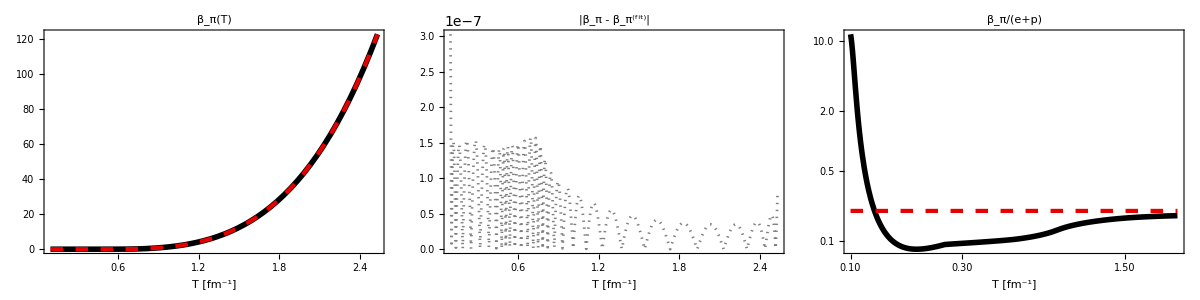

(-0.00030541207614527305 + 0.007861001974129155*T - 0.039760270871660224*Power(T,2) - 0.8085354595515646*Power(T,3) + 14.593877278234496*Power(T,4) - 
     113.21643371711893*Power(T,5) + 540.9234907375336*Power(T,6) - 1771.8920968315786*Power(T,7) + 4161.217880392231*Power(T,8) - 7115.896896471818*Power(T,9) + 
     8825.389586440731*Power(T,10) - 7757.6613865375175*Power(T,11) + 4595.643217605835*Power(T,12) - 1650.611265687417*Power(T,13) + 272.46357248088174*Power(T,14))/
   (9.037486761389047 - 103.5134926840149*T + 540.4664117866125*Power(T,2) - 1712.311561865406*Power(T,3) + 3687.6824561801272*Power(T,4) - 5704.80046476129*Power(T,5) + 
     6491.319088148271*Power(T,6) - 5436.977027878278*Power(T,7) + 3287.126109110171*Power(T,8) - 1380.245297906529*Power(T,9) + 384.77027582170484*Power(T,10) - 
     73.35613170371603*Power(T,11) + 12.018784984378653*Power(T,12) - 1.1964052741761402*Power(T,13) + 0.05462798322107767*Power(T,14))

```mathematica
betapiDataRaw=Import[wd<>"/betapiplot.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];
betapi = Interpolation[betapiData[[All,{1,2}]]];
n = 14;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapiconformal[T_]=0.2*(efit[T]+Pfit[T]);

Grid[{{Plot[{betapi[T],betapifit[T]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{betapi[T]/(efit[T]+Pfit[T]),betapiconformal[T]/(efit[T]+Pfit[T])},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
betapifit[T]//CForm
```

122.693

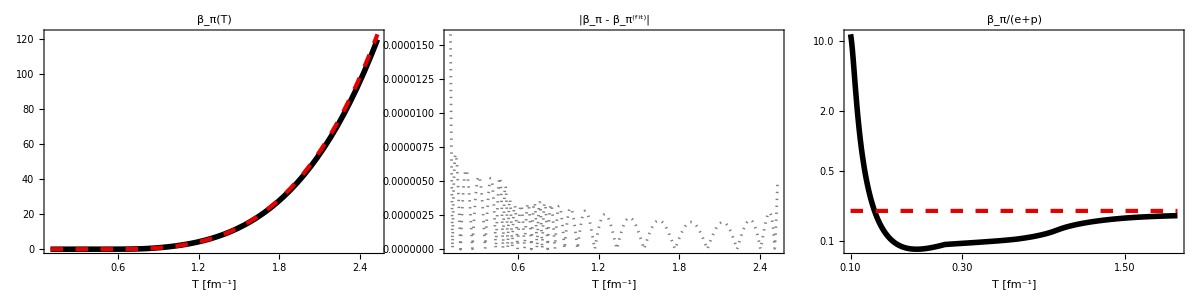

(0.001680656653815483 - 0.05705165502623733*T + 0.8438362180045873*Power(T,2) - 7.248762012039386*Power(T,3) + 40.489076904877365*Power(T,4) - 155.2015148490441*Power(T,5) + 
     419.6917891883335*Power(T,6) - 809.7562905973871*Power(T,7) + 1111.085390633557*Power(T,8) - 1061.8315461324846*Power(T,9) + 673.5303502063235*Power(T,10) - 
     255.53441424946044*Power(T,11) + 44.00311004757146*Power(T,12))/
   (1.9604428328737935 - 20.061333884163847*T + 90.55126386779529*Power(T,2) - 237.3248738733554*Power(T,3) + 399.5265859490588*Power(T,4) - 450.35773144929476*Power(T,5) + 
     343.2554024028255*Power(T,6) - 175.20473607521743*Power(T,7) + 59.648079556993025*Power(T,8) - 14.659364927694078*Power(T,9) + 3.026014542655646*Power(T,10) - 
     0.3696369881821592*Power(T,11) + 0.02027638952505763*Power(T,12))

```mathematica
betapiDataRaw=Import[wd<>"/betapiplot.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];
betapi = Interpolation[betapiData[[All,{1,2}]]];
n = 12;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapiconformal[T_]=0.2*(efit[T]+Pfit[T]);

betapifit[temp[[450]]]

betapiold[T_]=(8.611704298094825*10^-6-0.001405354006113392*T+0.059924402660583354*T^2-1.1252821226321765*T^3+11.505088678768702*T^4-72.86243933500441*T^5+312.67652000568955*T^6-919.4553300642775*T^7+1851.880055174282*T^8-2520.2910195876684*T^9+2228.4719999229687*T^10-1163.3696941415265*T^11+275.1649200477449*T^12)/(4.814184219646834-23.427763291345297*T+78.10907293901035*T^2-220.9834748507111*T^3+463.6211365026477*T^4-658.0962754530466*T^5+604.0491642749903*T^6-329.15455711633166*T^7+83.03984882593176*T^8-0.34262854377950497*T^9+0.03765047242502595*T^10-0.0024572359354327667*T^11+0.0000720828838022736*T^12);

Grid[{{Plot[{betapiold[T],betapifit[T]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]]},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{betapi[T]/(efit[T]+Pfit[T]),betapiconformal[T]/(efit[T]+Pfit[T])},{T,0.1,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
betapifit[T]//CForm
```

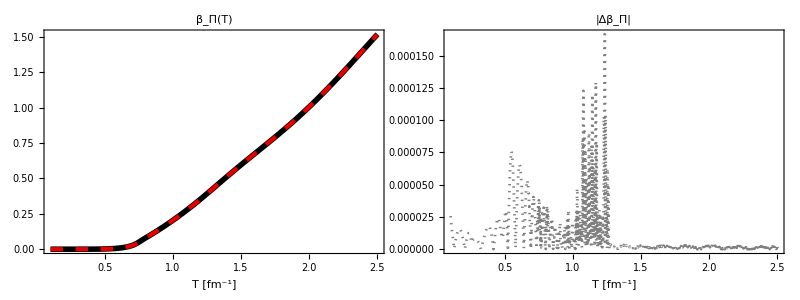

(0.04257847942110692 - 1.029190951154428*T + 10.462159871584094*Power(T,2) - 59.957855487223505*Power(T,3) + 218.6269588101918*Power(T,4) - 538.5992850621136*Power(T,5) + 
     924.5215738305378*Power(T,6) - 1120.0483931078222*Power(T,7) + 955.6903752460619*Power(T,8) - 563.3678416508982*Power(T,9) + 219.14157243961108*Power(T,10) - 
     50.843428950887855*Power(T,11) + 5.361123078976883*Power(T,12))/
   (176.17678351240284 - 1794.8043339933888*T + 8318.300742792633*Power(T,2) - 23171.90716019679*Power(T,3) + 43168.62628403139*Power(T,4) - 56603.44901553513*Power(T,5) + 
     53509.166015337934*Power(T,6) - 36710.399184192196*Power(T,7) + 18126.951232549065*Power(T,8) - 6281.369031330143*Power(T,9) + 1451.4883572413073*Power(T,10) - 
     201.6697089985485*Power(T,11) + 12.890715356154146*Power(T,12))

```mathematica
(* betabulk =5.0*betapi/3.0-cs2*(e+p)+cs2*mdmdT*I11 *)

I11DataRaw=Import[wd<>"/betabulkplot.dat"];
I11Data= Take[I11DataRaw,{2,Length[I11DataRaw]}];
I11 = Interpolation[I11Data[[All,{1,2}]]];


betabulk[T_]=5.0/3.0*betapi[T]+cs2fit[efit[T]]*(mdmdTQuasi[T]*I11[T]-(efit[T]+Pfit[T]));

betabulkData=Table[{T,betabulk[T]},{T,0.1,0.99temp[[450]],0.001}];

n = 12;
betabulkfit[T_]=rationalPolyFit[betabulkData,n,n]/.{x->T};


betabulkold[T_]=(0.057187918268175174-2.5795110808844144*T+31.966143337661794*T^2-186.97202223464143*T^3+632.9739160169219*T^4-1356.8644912535221*T^5+1937.6556428262882*T^6-1901.4144609887912*T^7+1305.7115016142484*T^8-632.7107309491553*T^9+215.7883928137199*T^10-50.783337922429304*T^11+7.882963305898372*T^12-0.7302386364254765*T^13+0.031006456705249083*T^14)/(2168.5818494848654-17367.372494454743*T+62866.89323544513*T^2-136008.52657020878*T^3+196076.0893015133*T^4-198954.9682758633*T^5+146384.87731197142*T^6-79310.95783243925*T^7+31803.091369445476*T^8-9398.242646642117*T^9+2016.6245278736917*T^10-304.98512854363526*T^11+30.758339605713708*T^12-1.852389925261096*T^13+0.05027444936020055*T^14);

betabulkconformal[T_]=14.55*(1.0/3.0-cs2fit[T])^2*(efit[T]+Pfit[T]);


Grid[{{
Plot[{betabulk[T],betabulkfit[T]},{T,0.1,0.99temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["β_Π(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betabulk[T]-betabulkfit[T]]},{T,0.1,0.99temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δβ_Π|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
(*,Plot[{betabulkfit[T]/(efit[T]+Pfit[T]),betabulkconformal[T]/(efit[T]+Pfit[T])},{T,temp[[1]],temp[[400]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]*)}}]

betabulkfit[T]//CForm
```